## Задание 1.

Спроектируйте и создайте функции для построения выпуклой оболочки заданного множества точек плоскости с использованием алгоритма Джарвиса . Проведите тестирование .

```mathematica
ClearAll[NamedQ,𝔨𝔪];
(** Атрибуты и описание **)
𝔨𝔪::usage="Knowledge base «computer mathematics»";
SetAttributes[𝔨𝔪,{Protected,ReadProtected}];
NamedQ::usage="Check: is there a name of tested equations";
NamedQ[n1_,n2__]:=And[NamedQ[n1],NamedQ[n2]];
SetAttributes[NamedQ,Listable];
```

```mathematica
ClearAll[kmPoint];
(** Атрибуты и описание **)
SetAttributes[kmPoint,ReadProtected];
kmPoint::usage="Point on the surface";
(** Свойства **)
NamedQ[kmPoint[𝔨𝔪,id_String,___]]^:=id≠"";
kmPoint[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmPoint[𝔨𝔪,id_String,___]["id"]:=If[id=="","Point",id];
(** Конструкторы **)
kmPoint[id_String,coord:{_,_}]:=kmPoint[𝔨𝔪,id,coord];
kmPoint[coord:{_,_}]:=kmPoint[𝔨𝔪,"",coord];
kmPoint[{L1_kmLine,L2_kmLine}]:=kmPoint[#[[2]]&/@(First@NSolve@Through[{L1,L2}@"equ"])]
(** Декораторы **)
Format[P_kmPoint,StandardForm]:=Row@{P["id"],"(",Row[P["coord"],","],")"};
```

```mathematica
ClearAll[kmVector];
(** Атрибуты и описание **)
SetAttributes[kmVector,ReadProtected];
kmVector::usage="Vector on the surface";
(** Свойства **)
NamedQ[kmVector[𝔨𝔪,id_String,___]]^:=id≠"";
kmVector[𝔨𝔪,id_String,___]["id"]:=If[id=="","Vector",id];
kmVector[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmVector[𝔨𝔪,_String,coord_List,___]["norm"]:=Sqrt[Plus@@(coord*coord)];
(** Конструкторы **)
kmVector[id_String,coord_List]:=kmVector[𝔨𝔪,id,coord];
kmVector[coord_List]:=kmVector[𝔨𝔪,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
MakeBoxes[V_kmVector,StandardForm]^:=TemplateBox[{V@"id",
RowBox@Riffle[MakeBoxes[#,StandardForm]&/@V["coord"],","]
},"Point2D",
DisplayFunction:>(RowBox@{OverscriptBox[#1,"⇀"],"(",#2,")"}&),
InterpretationFunction->(RowBox@{"{",#2,"}"}&),
Tooltip->Automatic];
```

```mathematica
ClearAll[kmLine];
(** Атрибуты и описание **)
SetAttributes[kmLine,ReadProtected];
kmLine::usage="Line on the surface";
(** Свойства **)
NamedQ[kmLine[𝔨𝔪,id_String,___]]^:=id≠"";
kmLine[𝔨𝔪,id_String,___]["id"]:=If[id=="","Line",id];
kmLine[𝔨𝔪,_String,coef_List,___]["coef"]:=coef;
kmLine[𝔨𝔪,_String,coef_List,___]["equ",vars:{_Symbol,_Symbol}:{x,y}]:=
coef.Append[vars,1]==0;
(** Конструкторы **)
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars];
kmLine[id_String,A_. x_+B_.y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[𝔨𝔪,id,{A,B,C}]/;¬PossibleZeroQ[Abs@A+Abs@B];
kmLine[id_String,A_. x_+C_.==0,{x_Symbol,_Symbol}]:=kmLine[𝔨𝔪,id,{A,0,C}];
kmLine[id_String,B_. y_+C_.==0,{_Symbol,y_Symbol}]:=kmLine[𝔨𝔪,id,{0,B,C}];
kmLine[id_String,P_kmPoint,Dir_kmVector]:=kmLine[𝔨𝔪,id,
Append[#,-#.P["coord"]]&[({{0, -1}, {1, 0}}).Dir["coord"]]];
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[
If[NamedQ[P,Dir],StringJoin[P@"id",Dir@"id"],""],P,Dir];
kmLine[id_String,P1_kmPoint,P2_kmPoint]:=kmLine[id,P1,kmVector["",P1,P2]]
kmLine[{P1_kmPoint,P2_kmPoint}]:=kmLine[P1,kmVector[P2@"id",P1,P2]]
kmLine[id_String,segment_kmSegment]:=Block[{x1=(segment["end1Coord"])["coord"][[1]],y1=(segment["end1Coord"])["coord"][[2]],x2=(segment["end2Coord"])["coord"][[1]],y2=(segment["end2Coord"])["coord"][[2]]},kmLine[id,(y1-y2)x+(x2-x1)y+(x1*y2-x2*y1)==0,{x,y}]]
kmLine[segment_kmSegment]:=Block[{x1=(segment["end1Coord"])["coord"][[1]],y1=(segment["end1Coord"])["coord"][[2]],x2=(segment["end2Coord"])["coord"][[1]],y2=(segment["end2Coord"])["coord"][[2]]},kmLine[(y1-y2)x+(x2-x1)y+(x1*y2-x2*y1)==0,{x,y}]]
(** Декораторы **)
Format[L_kmLine,StandardForm]:=Row@{L@"id",": ",L@"equ"};
```

```mathematica
ClearAll[kmSegment];
(** Атрибуты и описание **)
SetAttributes[kmSegment,ReadProtected];
kmLine::usage="Отрезок на плоскости";
(** Свойства **)
NamedQ[kmSegment[𝔨𝔪,id_String,___]]^:=id≠"";
kmSegment[𝔨𝔪,id_String,___]["id"]:=If[id=="","Segment",id];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["coords"]:=kmPoint[#]&/@endCoords;
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["end1Coord"]:=Module[{x1=endCoords[[1,1]],y1=endCoords[[1,2]],x2=endCoords[[2,1]],y2=endCoords[[2,2]]},If[x1<x2||y1<y2,kmPoint[{x1,y1}],kmPoint[{x2,y2}]]];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["end2Coord"]:=Module[{x1=endCoords[[1,1]],y1=endCoords[[1,2]],x2=endCoords[[2,1]],y2=endCoords[[2,2]]},If[x1<x2||y1<y2,kmPoint[{x2,y2}],kmPoint[{x1,y1}]]];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["len"]:=Sqrt[Plus@@((endCoords[[1]]-endCoords[[2]])^2)]
(** Конструкторы **)
kmSegment[id_String,endsCoords:{{_,_},{_,_}}]:=kmSegment[𝔨𝔪,id,endsCoords];
kmSegment[endsCoords:{{_,_},{_,_}}]:=kmSegment[𝔨𝔪,"",endsCoords];
kmSegment[id_String,P0_kmPoint,P1_kmPoint]:=kmSegment[id,{P1@"coord",P0@"coord"}];
kmSegment[P0_kmPoint,P1_kmPoint]:=kmSegment[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
Format[Segment_kmSegment,StandardForm]:=Row@{Segment@"id",": ",Segment@"coords"};
(**Отображение отрезка на рисунке**)
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[
ReplaceAll[gp,{
P_kmPoint:>Tooltip[Point@P@"coord",Style[Format[P,StandardForm],Large]],
L_kmLine:>Tooltip[
InfiniteLine@Through@getTwoLinePoints[L]@"coord",
Style[Format[L,StandardForm],Large]],
Segment_kmSegment:>Tooltip[Line[{Segment@"end1Coord",Segment@"end2Coord"}]]
}],
opts];
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,2.06503-5.8414),Point(,,8.470296.15967),Point(,,3.344978.6679),Point(,,2.884682.45096),Point(,,-9.565698.25928),Point(,,-9.314690.177054),Point(,,-1.070394.64609),Point(,,6.892127.11934),Point(,,-4.9768-0.377115),Point(,,-4.27193-8.01429),Point(,,-5.111068.27395),Point(,,-7.28148-7.44068),Point(,,8.95191-1.51886),Point(,,-2.319241.45248),Point(,,3.614713.26242),Point(,,-3.71518-5.54564),Point(,,1.28526-4.07032),Point(,,-6.521591.60805),Point(,,-8.59424-9.70219),Point(,,-5.725161.1717)}

```mathematica
getTriangleAlgebraicSquare[points_List]:=Module[{a=points[[1]]["coord"],b=points[[2]]["coord"],c=points[[3]]["coord"]},1/2 Det[{b-a,c-a}]]
```

```mathematica
isPointOnLine[Line_kmLine,P_kmPoint]:=Line["equ"]/.{x->P["coord"][[1]],y->P["coord"][[2]]}
```

```mathematica
Unprotect[Unequal];
```

```mathematica
Unequal[Point1_kmPoint,Point2_kmPoint]:=Point1["coord"]!=Point2["coord"]
```

Важно закинуть стартовую точку в конец Q.

```mathematica
getStartPoint[Q_List]:=Module[{StartPoint=Q[[1]]},
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<=StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
];
Return@StartPoint
]
```

```mathematica
moveToEndOfList[lst_List,obj_]:=Append[DeleteCases[lst,obj],obj]
```

```mathematica
getParameter[Segment_kmSegment,P_kmPoint]:=Block[{x0=Segment["end1Coord"]["coord"][[1]],x1=Segment["end2Coord"]["coord"][[1]],
y0=Segment["end1Coord"]["coord"][[2]],y1=Segment["end2Coord"]["coord"][[2]]},
If[x1-x0==0,(First@First@NSolve[(y1-y0)*t+y0==P["coord"][[2]],t])[[2]],(First@First@NSolve[(x1-x0)*t+x0==P["coord"][[1]],t])[[2]]]]
```

```mathematica
CH[pointsList_List]:=Module[{i=1,Q=pointsList,StartPoint,CurrentPoint,NextPoint,algebraicSquare,L={}},
StartPoint=getStartPoint[Q];
L=AppendTo[L,StartPoint];
Q=moveToEndOfList[Q,StartPoint];
CurrentPoint=StartPoint;
NextPoint=Q[[1]];
While[NextPoint!=StartPoint,
Do[
If[
isPointOnLine[
kmLine[{CurrentPoint,NextPoint}],i
]
&&
kmSegment[CurrentPoint,i]["len"]>kmSegment[CurrentPoint,NextPoint]["len"],NextPoint=i,
algebraicSquare=getTriangleAlgebraicSquare[{CurrentPoint,i,NextPoint}];
If[algebraicSquare>0,NextPoint=i]
],
{i,DeleteCases[Q,NextPoint]}
];
Q=DeleteCases[Q,NextPoint];
L=AppendTo[L,NextPoint];
If[NextPoint==StartPoint,Return@L];
CurrentPoint=NextPoint;
NextPoint=Q[[1]]
];
]
```

Проверяю

```mathematica
Q1=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,5.86906-9.71619),Point(,,-6.64216-1.87941),Point(,,-2.91153-8.71202),Point(,,9.649077.29881),Point(,,-9.22216-7.21065),Point(,,-7.04641-1.54761),Point(,,6.920288.67586),Point(,,-9.93959-6.81352),Point(,,-2.595753.55932),Point(,,-4.651139.90314),Point(,,-9.46740.318974),Point(,,-3.973720.121891),Point(,,-9.753861.19497),Point(,,3.61982-4.74759),Point(,,-4.474098.30787),Point(,,3.898718.06792),Point(,,7.18558-5.82104),Point(,,-0.2692696.8958),Point(,,8.903895.57002),Point(,,-1.05787-9.96965)}

```mathematica
res1=CH[Q1]
```

{Point(,,-1.05787-9.96965),Point(,,5.86906-9.71619),Point(,,7.18558-5.82104),Point(,,9.649077.29881),Point(,,6.920288.67586),Point(,,-4.651139.90314),Point(,,-9.753861.19497),Point(,,-9.93959-6.81352),Point(,,-9.22216-7.21065),Point(,,-1.05787-9.96965)}

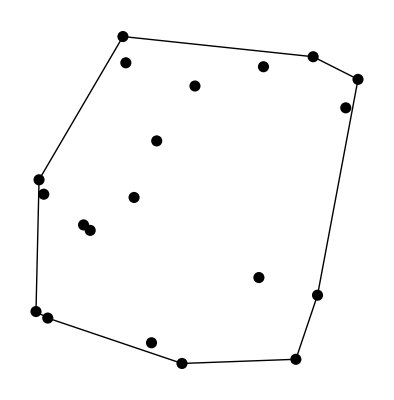

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q1,Line[{#["coord"]&/@res1}]}]
```

```mathematica
Q2={kmPoint[{6,3}],kmPoint[{6,5}],kmPoint[{3,5}],kmPoint[{6,1}],kmPoint[{1,2}],kmPoint[{1,1}],kmPoint[{3,1}],kmPoint[{4,6}],kmPoint[{2,4}],kmPoint[{6,5}],kmPoint[{5,1}],kmPoint[{1,3}]}
```

{Point(,,63),Point(,,65),Point(,,35),Point(,,61),Point(,,12),Point(,,11),Point(,,31),Point(,,46),Point(,,24),Point(,,65),Point(,,51),Point(,,13)}

```mathematica
res2=CH[Q2]
```

{Point(,,11),Point(,,61),Point(,,65),Point(,,46),Point(,,13),Point(,,11)}

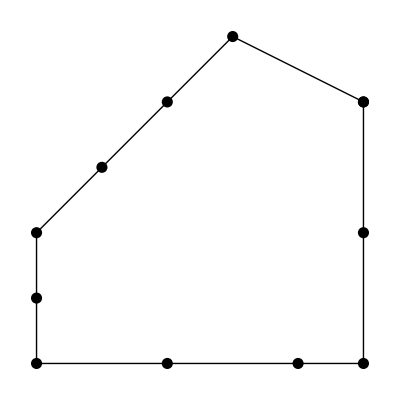

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q2,Line[{#["coord"]&/@res2}]}]
```

## Задание 2.

Спроектируйте и создайте функции для построения выпуклой оболочки заданного множества точек плоскости с использованием алгоритма Джарвиса . Проведите тестирование .

```mathematica
isGreater[StartPoint_kmPoint,Point1_kmPoint,Point2_kmPoint]:=getTriangleAlgebraicSquare[{StartPoint,Point2,Point1}]>0||And[isPointOnLine[kmLine[{StartPoint,Point1}],Point2],
kmSegment[StartPoint,Point2]["len"]>kmSegment[StartPoint,Point1]["len"]]
```

```mathematica
sortByPolarAngle[points_List]:=Module[
{StartPoint=getStartPoint[points],sorted=points,flag},
sorted=DeleteCases[sorted,StartPoint];
sorted=Insert[sorted,StartPoint,1];
For[
i=1,1<=Length@sorted,i++,
flag=True;
For[
j=2,j<Length@sorted,j++,
If[
isGreater[StartPoint,sorted[[j]],sorted[[j+1]]],
sorted=Insert[sorted,sorted[[j]],j+2];
sorted=Delete[sorted,j];
flag=False;
]
];
If[flag,Return@sorted]
];
]
```

Проверяю

```mathematica
sortByPolarAngle[{kmPoint[{1,2}],kmPoint[{5,1}],kmPoint[{9,4}],kmPoint[{-6,-1}],kmPoint[{0,3}]}]
```

{Point(,,-6-1),Point(,,03),Point(,,12),Point(,,94),Point(,,51)}

```mathematica
sortByPolarAngle[{kmPoint[{8,6}],kmPoint[{-1,2}],kmPoint[{3,4}],kmPoint[{12,2}],kmPoint[{5,4}],kmPoint[{-1,0}],kmPoint[{-1,4}],kmPoint[{-1,3}],kmPoint[{8,2}],kmPoint[{10,4}],kmPoint[{-2,6}]}]
```

{Point(,,-10),Point(,,122),Point(,,82),Point(,,104),Point(,,86),Point(,,54),Point(,,34),Point(,,-14),Point(,,-13),Point(,,-12),Point(,,-26)}